```mathematica
(*From the paper hand calcuation before substituting p1=3/4p1 and p2=3/4p2*)
c1=Sqrt[(1-p1)^2+p1^2/9]
c2=Sqrt[(1-p1)2p1/3]
c3=Sqrt[2]p1 /3
c4=Sqrt[2]p1/3
```

√((1-p1)^2+p1^2/9)

√(2/3) √((1-p1) p1)

(√2 p1)/3

(√2 p1)/3

```mathematica
FullSimplify[(c1^2+c2^2+c3^2+c4^2)]
```

1+4/9 p1 (-3+2 p1)

```mathematica
(*Sqrt of coefficients for single effective noise map on one qubit in the bell state.*)
c1=Sqrt[(1-p1)^2+p1^2/9]/.{p1->3/4p1}
c2=Sqrt[(1-p1)2p1/3]/.{p1->3/4p1}
c3=Sqrt[2]p1 /3/.{p1->3/4p1}
c4=Sqrt[2]p1/3/.{p1->3/4p1}
```

√((1-(3 p1)/4)^2+p1^2/16)

(√((1-(3 p1)/4) p1))/(√2)

p1/(2 √2)

p1/(2 √2)

```mathematica
(*For 1 qubit*)
postselectRate1=FullSimplify[(c1^2+c2^2+c3^2+c4^2)]
fidelity1=FullSimplify[c1^2/postselectRate1] (*Only the identity term contributes.*)
```

1+1/2 (-2+p1) p1

(8+p1 (-12+5 p1))/(8+4 (-2+p1) p1)

```mathematica
(*comparing 1 pcs X with no pcs*)
fidelity1/.p1->.1 
FullSimplify[FullSimplify[c1^2+c2^4+c3^2+c4^2]/.p1->.1]
```

0.946133

0.860889

```mathematica
(*For both qubits. The other half undergo single qubit depolarizing channels with error probs of p2*)
postselectRate2=postselectRate1/.p1->p2
d1=c1/.p1->p2;
d2=c2/.p1->p2;
d3=c3/.p1->p2;
d4=c4/.p1->p2;
postselectRate12=FullSimplify[postselectRate1*postselectRate2] 
fidelity12=FullSimplify[(c1^2 d1^2+c2^2 d2^2+c3^2 d3^2+c4^2 d4^2)/postselectRate12](*The phi+ is stabilized by XX and ZZ. Additionally YY only introduces a global phase.*)
```

1+1/2 (-2+p2) p2

1/4 (2+(-2+p1) p1) (2+(-2+p2) p2)

(16+2 p1 (-12+5 p1)-24 p2+2 (20-9 p1) p1 p2+(10+9 (-2+p1) p1) p2^2)/(4 (2+(-2+p1) p1) (2+(-2+p2) p2))

```mathematica
(*p1=p2=p*)
postrEqual12=FullSimplify[postselectRate12/.{p1->p,p2->p}]
fidelityEqual12=FullSimplify[fidelity12/.{p1->p,p2->p}]
```

1/4 (2+(-2+p) p)^2

(4+3 (-2+p) p)^2/(4 (2+(-2+p) p)^2)

```mathematica
(*In terms of initial F*)
fidelityInitialF12=FullSimplify[fidelityEqual12/.{p->1/3 (3-√3 √(-1+4 F))}] (*these initial fidelities are calculated in file pccs_x_checks_fidelity_post_rate.nb*)
postrInitialF12=FullSimplify[postrEqual12/.{p->1/3 (3-√3 √(-1+4 F))}]
fidelityInitialF12=FullSimplify[fidelityEqual12/.{p->1/3 (3+√3 √(-1+4 F))}] (*these initial fidelities are calculated in file pccs_x_checks_fidelity_post_rate.nb*)
postrInitialF12=FullSimplify[postrEqual12/.{p->1/3 (3+√3 √(-1+4 F))}]
```

(9 F^2)/(1+2 F)^2

1/9 (1+2 F)^2

(9 F^2)/(1+2 F)^2

1/9 (1+2 F)^2

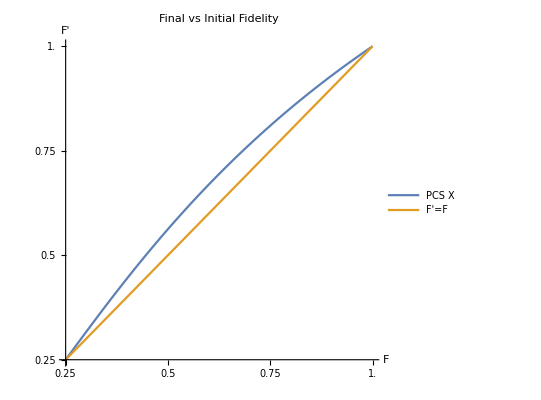

```mathematica
Plot[{fidelityInitialF12, F},{F,1/4,1}, PlotLegends->Placed[{"PCS X", "F'=F"},{Right, Center}], AxesLabel->{"F", "F'"}, AspectRatio->1,  PlotLabel->"Final vs Initial Fidelity", Ticks->{Range[1/4,1,0.25],Range[1/4,1,0.25]}]
```

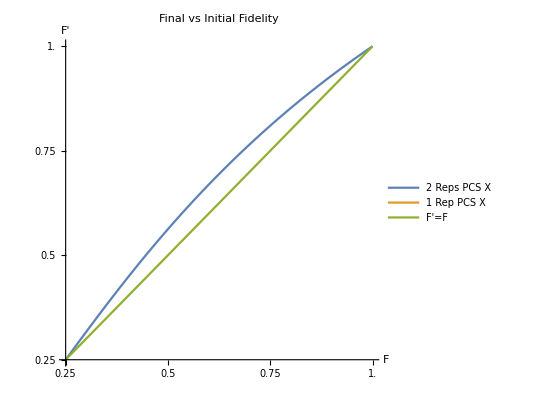

```mathematica
fid[F_]:=fidelityInitialF12
Plot[{fid[fid[fidelityInitialF12]], fidelityInitialF, F},{F,1/4,1},  PlotLegends->Placed[{"2 Reps PCS X","1 Rep PCS X", "F'=F"},{Right, Center}], AxesLabel->{"F", "F'"}, AspectRatio->1, PlotLabel->"Final vs Initial Fidelity", Ticks->{Range[1/4,1,0.25],Range[1/4,1,0.25]}]
```